# Optimal Control

## One point rolling using 3DoF Arm

Adam Barber

## Tracking a trajectory while balancing an object through a one point rolling constraint.

```mathematica
Quit
```

Iteration Number 2 Begin

-7.2185

Optimization Complete

The final cost is = 6.61863×10^9

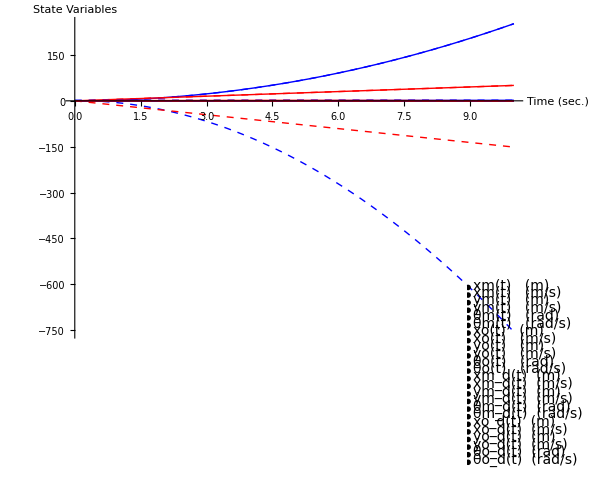

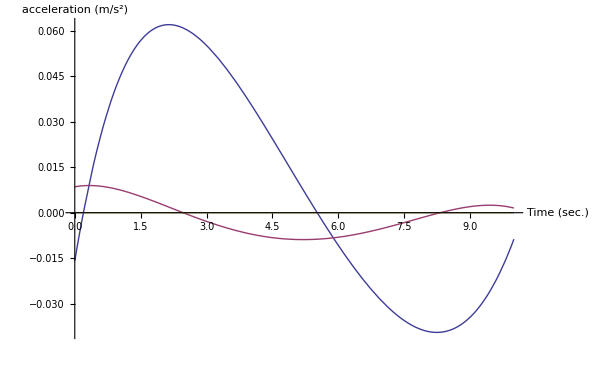

```mathematica
(*Just some set up*)
Needs["PlotLegends`"]
Off[NIntegrate::"slwcon"]
Off[NIntegrate::"ncvb"]
(*First let's define the system variables*)
numStates = 12;
numControls = 3;
(* State variables in this care are: xm[t], xm'[t], ym[t], ym'[t], θm[t], θm'[t], xo[t], xo'[t], yo[t], yo'[t], θo[t], θo'[t]. All are measured in the world frame*)
state[t_] := Table[{x[i][t]},{i,1,numStates}]; 
(* Controls are xm''[t] ym''[t], and θm''[t] of the base, which we can specify*)
controls[t_]:=Table[{u[i][t]},{i,1,numControls}]; 

(*Define the system dynamics*)
(*Dynamics are calculated using the my stuff by hand.*)
(*xodd[x_,u_] := 1/(4 (lc+3 lo))(4 ((lc+3 lo) (lm-s1) Cos[thm]-3 wm wo Cos[thm-tho] Cos[tho]+(lc+3 lo) wm Sin[thm]-3 lo wm Cos[thm-tho] Sin[tho]+3 (lm-s1) Sin[thm-tho] (wo Cos[tho]+lo Sin[tho])) thmd^2+(-(4 lc lo+9 lo^2+9 lo wo+12 wo^2) Cos[tho]-3 lo (lo+wo) Cos[3 tho]+(4 lc wo+3 lo (-lo+wo)) Sin[tho]+3 lo (-lo+wo) Sin[3 tho]) thod^2+2 ((2 lc+3 lo+3 lo Cos[2 tho]-3 wo Sin[2 tho]) xmdd+6 Cos[tho] (wo Cos[tho]+lo Sin[tho]) (g+ymdd)-2 ((lc+3 lo) wm Cos[thm]-(lc+3 lo) (lm-s1) Sin[thm]+3 wm wo Cos[tho] Sin[thm-tho]+3 lo wm Sin[thm-tho] Sin[tho]+3 (lm-s1) Cos[thm-tho] (wo Cos[tho]+lo Sin[tho])) thmdd))/.
{xmdd -> Flatten[u[[1]][t]][[1]](*Flatten[controls[t]⟦1⟧]⟦1⟧*), ymdd -> Flatten[u[[2]][t]][[1]](*Flatten[controls[t]⟦2⟧]⟦1⟧*), 
thmdd -> Flatten[u[[3]][t]][[1]](*Flatten[controls[t]⟦3⟧]⟦1⟧*), 
xm  -> Flatten[x⟦1⟧]⟦1⟧, xmd  -> Flatten[x⟦2⟧]⟦1⟧, ym  -> Flatten[x⟦3⟧]⟦1⟧, ymd  -> Flatten[x⟦4⟧]⟦1⟧,thm  -> Flatten[x⟦5⟧]⟦1⟧, thmd  -> Flatten[x⟦6⟧]⟦1⟧, xo  -> Flatten[x⟦7⟧]⟦1⟧,xod  -> Flatten[x⟦8⟧]⟦1⟧,yo  -> Flatten[x⟦9⟧]⟦1⟧,yod  -> Flatten[x⟦10⟧]⟦1⟧, tho  -> Flatten[x⟦11⟧]⟦1⟧, thod  -> Flatten[x⟦12⟧]⟦1⟧} /.Thread[Flatten[controls[t]]-> Flatten[u]];*)
xodd[x_,u_]:=(-3 g Sin[tho + ArcTan[lo,wo] - π/2] (wo Cos[tho]+lo Sin[tho])+(lc (lm-s1) Cos[thm]+3 (-lm lo+lo s1+wm wo) Cos[thm-tho] Sin[tho + ArcTan[wo/lo] - π/2]+lc wm Sin[thm]-3 (lo wm+lm wo-s1 wo) Sin[tho + ArcTan[wo/lo] - π/2] Sin[thm-tho]) thmd^2+(-lc lo Cos[tho]+3 (lo^2+wo^2) Sin[tho + ArcTan[wo/lo] - π/2]+lc wo Sin[tho]) thod^2+lc (-(wm Cos[thm]+(-lm+s1) Sin[thm]) thmdd+xmdd)+3 Sin[tho + ArcTan[wo/lo] - π/2] (((lo wm+lm wo-s1 wo) Cos[thm-tho]+(-lm lo+lo s1+wm wo) Sin[thm-tho]) thmdd+(-lo Cos[tho]+wo Sin[tho]) xmdd-(wo Cos[tho]+lo Sin[tho]) ymdd))/(lc+3 wo Cos[tho + ArcTan[wo/lo] - π/2-tho]-3 lo Sin[tho + ArcTan[wo/lo] - π/2-tho])/.
{xmdd -> Flatten[u[[1]][t]][[1]](*Flatten[controls[t]⟦1⟧]⟦1⟧*), ymdd -> Flatten[u[[2]][t]][[1]](*Flatten[controls[t]⟦2⟧]⟦1⟧*), 
thmdd -> Flatten[u[[3]][t]][[1]](*Flatten[controls[t]⟦3⟧]⟦1⟧*), 
xm  -> Flatten[x⟦1⟧]⟦1⟧, xmd  -> Flatten[x⟦2⟧]⟦1⟧, ym  -> Flatten[x⟦3⟧]⟦1⟧, ymd  -> Flatten[x⟦4⟧]⟦1⟧,thm  -> Flatten[x⟦5⟧]⟦1⟧, thmd  -> Flatten[x⟦6⟧]⟦1⟧, xo  -> Flatten[x⟦7⟧]⟦1⟧,xod  -> Flatten[x⟦8⟧]⟦1⟧,yo  -> Flatten[x⟦9⟧]⟦1⟧,yod  -> Flatten[x⟦10⟧]⟦1⟧, tho  -> Flatten[x⟦11⟧]⟦1⟧, thod  -> Flatten[x⟦12⟧]⟦1⟧} /.Thread[Flatten[controls[t]]-> Flatten[u]];
(*yodd[x_,u_] := 1/(2 (lc+3 lo))(6 g Cos[tho] (-lo Cos[tho]+wo Sin[tho])+1/2 (-4 ((lc+3 lo) wm Cos[thm]+3 wm Cos[thm-tho] (-lo Cos[tho]+wo Sin[tho])-(lm-s1) ((lc+3 lo) Sin[thm]+3 Sin[thm-tho] (-lo Cos[tho]+wo Sin[tho]))) thmd^2+(-(3 lo (lo-wo)+4 lc (lo+wo)) Cos[tho]+3 lo (lo-wo) Cos[3 tho]-3 (lo^2+lo wo+4 wo^2) Sin[tho]-3 lo (lo+wo) Sin[3 tho]) thod^2+2 (6 Sin[tho] (lo Cos[tho]-wo Sin[tho]) xmdd+2 (lc+3 Sin[tho] (wo Cos[tho]+lo Sin[tho])) ymdd-2 ((lc+3 lo) (lm-s1) Cos[thm]+lc wm Sin[thm]+3 wm wo Sin[thm-tho] Sin[tho]+3 Cos[thm-tho] (lo (-lm+s1) Cos[tho]+(lo wm+lm wo-s1 wo) Sin[tho])) thmdd)))/.{xmdd -> Flatten[u[[1]][t]][[1]](*Flatten[controls[t]⟦1⟧]⟦1⟧*), 
ymdd -> Flatten[u[[2]][t]][[1]](*Flatten[controls[t]⟦2⟧]⟦1⟧*), 
thmdd -> Flatten[u[[3]][t]][[1]](*Flatten[controls[t]⟦3⟧]⟦1⟧*), 
xm  -> Flatten[x⟦1⟧]⟦1⟧, xmd  -> Flatten[x⟦2⟧]⟦1⟧, ym  -> Flatten[x⟦3⟧]⟦1⟧, ymd  -> Flatten[x⟦4⟧]⟦1⟧,thm  -> Flatten[x⟦5⟧]⟦1⟧, thmd  -> Flatten[x⟦6⟧]⟦1⟧, xo  -> Flatten[x⟦7⟧]⟦1⟧,xod  -> Flatten[x⟦8⟧]⟦1⟧,yo  -> Flatten[x⟦9⟧]⟦1⟧,yod  -> Flatten[x⟦10⟧]⟦1⟧, tho  -> Flatten[x⟦11⟧]⟦1⟧, thod  -> Flatten[x⟦12⟧]⟦1⟧} /.Thread[Flatten[controls[t]]-> Flatten[u]];*)
yodd[x_,u_]:= (3 g Sin[tho + ArcTan[wo/lo] - π/2] (lo Cos[tho]-wo Sin[tho])+(-lc wm Cos[thm]+lc (lm-s1) Sin[thm]+3 Cos[tho + ArcTan[wo/lo] - π/2] Cos[tho] ((lm lo-lo s1-wm wo) Cos[thm]+(lo wm+lm wo-s1 wo) Sin[thm])-3 Cos[tho + ArcTan[wo/lo] - π/2] ((lo wm+lm wo-s1 wo) Cos[thm]+(-lm lo+lo s1+wm wo) Sin[thm]) Sin[tho]) thmd^2-(3 (lo^2+wo^2) Cos[tho + ArcTan[wo/lo] - π/2]+lc wo Cos[tho]+lc lo Sin[tho]) thod^2+lc (-((lm-s1) Cos[thm]+wm Sin[thm]) thmdd+ymdd)+3 Cos[tho + ArcTan[wo/lo] - π/2] Sin[tho] (((-lm lo+lo s1+wm wo) Cos[thm]-(lo wm+lm wo-s1 wo) Sin[thm]) thmdd-wo xmdd+lo ymdd)+3 Cos[tho + ArcTan[wo/lo] - π/2] Cos[tho] ((-(lo wm+lm wo-s1 wo) Cos[thm]+(lm lo-lo s1-wm wo) Sin[thm]) thmdd+lo xmdd+wo ymdd))/(lc+3 wo Cos[tho + ArcTan[wo/lo] - π/2-tho]-3 lo Sin[tho + ArcTan[wo/lo] - π/2-tho])/.
{xmdd -> Flatten[u[[1]][t]][[1]](*Flatten[controls[t]⟦1⟧]⟦1⟧*), ymdd -> Flatten[u[[2]][t]][[1]](*Flatten[controls[t]⟦2⟧]⟦1⟧*), 
thmdd -> Flatten[u[[3]][t]][[1]](*Flatten[controls[t]⟦3⟧]⟦1⟧*), 
xm  -> Flatten[x⟦1⟧]⟦1⟧, xmd  -> Flatten[x⟦2⟧]⟦1⟧, ym  -> Flatten[x⟦3⟧]⟦1⟧, ymd  -> Flatten[x⟦4⟧]⟦1⟧,thm  -> Flatten[x⟦5⟧]⟦1⟧, thmd  -> Flatten[x⟦6⟧]⟦1⟧, xo  -> Flatten[x⟦7⟧]⟦1⟧,xod  -> Flatten[x⟦8⟧]⟦1⟧,yo  -> Flatten[x⟦9⟧]⟦1⟧,yod  -> Flatten[x⟦10⟧]⟦1⟧, tho  -> Flatten[x⟦11⟧]⟦1⟧, thod  -> Flatten[x⟦12⟧]⟦1⟧} /.Thread[Flatten[controls[t]]-> Flatten[u]];
(*thodd[x_,u_] := 1/(2 (lc+3 lo))3 (2 (wm Cos[thm-tho]+(-lm+s1) Sin[thm-tho]) thmd^2+(lo+2 wo+lo Cos[2 tho]-lo Sin[2 tho]) thod^2+2 Sin[tho] xmdd-2 Cos[tho] (g+ymdd)+2 ((lm-s1) Cos[thm-tho]+wm Sin[thm-tho]) thmdd)/.
{xmdd -> Flatten[u[[1]][t]][[1]](*Flatten[controls[t]⟦1⟧]⟦1⟧*), 
ymdd -> Flatten[u[[2]][t]][[1]](*Flatten[controls[t]⟦2⟧]⟦1⟧*), 
thmdd -> Flatten[u[[3]][t]][[1]](*Flatten[controls[t]⟦3⟧]⟦1⟧*), 
xm  -> Flatten[x⟦1⟧]⟦1⟧, xmd  -> Flatten[x⟦2⟧]⟦1⟧, ym  -> Flatten[x⟦3⟧]⟦1⟧, ymd  -> Flatten[x⟦4⟧]⟦1⟧,thm  -> Flatten[x⟦5⟧]⟦1⟧, thmd  -> Flatten[x⟦6⟧]⟦1⟧, xo  -> Flatten[x⟦7⟧]⟦1⟧,xod  -> Flatten[x⟦8⟧]⟦1⟧,yo  -> Flatten[x⟦9⟧]⟦1⟧,yod  -> Flatten[x⟦10⟧]⟦1⟧, tho  -> Flatten[x⟦11⟧]⟦1⟧, thod  -> Flatten[x⟦12⟧]⟦1⟧} /.Thread[Flatten[controls[t]]-> Flatten[u]];*)
thodd[x_,u_] := -(3 (((-lm+s1) Cos[tho + ArcTan[wo/lo] - π/2-thm]+wm Sin[tho + ArcTan[wo/lo] - π/2-thm]) thmd^2+(lo Cos[tho + ArcTan[wo/lo] - π/2-tho]+wo Sin[tho + ArcTan[wo/lo] - π/2-tho]) thod^2+(wm Cos[tho + ArcTan[wo/lo] - π/2-thm]+(lm-s1) Sin[tho + ArcTan[wo/lo] - π/2-thm]) thmdd-Cos[tho + ArcTan[wo/lo] - π/2] xmdd[t]-Sin[tho + ArcTan[wo/lo] - π/2] (g+ymdd[t])))/(lc+3 wo Cos[tho + ArcTan[wo/lo] - π/2-tho]-3 lo Sin[tho + ArcTan[wo/lo] - π/2-tho])/.
{xmdd -> Flatten[u[[1]][t]][[1]](*Flatten[controls[t]⟦1⟧]⟦1⟧*), 
ymdd -> Flatten[u[[2]][t]][[1]](*Flatten[controls[t]⟦2⟧]⟦1⟧*), 
thmdd -> Flatten[u[[3]][t]][[1]](*Flatten[controls[t]⟦3⟧]⟦1⟧*), 
xm  -> Flatten[x⟦1⟧]⟦1⟧, xmd  -> Flatten[x⟦2⟧]⟦1⟧, ym  -> Flatten[x⟦3⟧]⟦1⟧, ymd  -> Flatten[x⟦4⟧]⟦1⟧,thm  -> Flatten[x⟦5⟧]⟦1⟧, thmd  -> Flatten[x⟦6⟧]⟦1⟧, xo  -> Flatten[x⟦7⟧]⟦1⟧,xod  -> Flatten[x⟦8⟧]⟦1⟧,yo  -> Flatten[x⟦9⟧]⟦1⟧,yod  -> Flatten[x⟦10⟧]⟦1⟧, tho  -> Flatten[x⟦11⟧]⟦1⟧, thod  -> Flatten[x⟦12⟧]⟦1⟧} /.Thread[Flatten[controls[t]]-> Flatten[u]];
f[x_,u_] := ({{Flatten[x⟦2⟧]⟦1⟧}, {Flatten[controls[t]⟦1⟧]⟦1⟧}, {Flatten[x⟦4⟧]⟦1⟧}, {Flatten[controls[t]⟦2⟧]⟦1⟧}, {Flatten[x⟦6⟧]⟦1⟧}, {Flatten[controls[t]⟦3⟧]⟦1⟧}, {Flatten[x⟦8⟧]⟦1⟧}, {Flatten[xodd[x,u]]⟦1⟧}, {Flatten[x⟦10⟧]⟦1⟧}, {Flatten[yodd[x,u]]⟦1⟧}, {Flatten[x⟦12⟧]⟦1⟧}, {Flatten[thodd[x,u]]⟦1⟧}})/.Thread[Flatten[controls[t]]-> Flatten[u]]; (*xm,xmd,ym,ymd,thm,thmd*)
(*f[x_,u_]:=({{Flatten[x⟦2⟧]⟦1⟧}, {Flatten[controls[t]⟦1⟧]⟦1⟧}, {Flatten[x⟦4⟧]⟦1⟧}, {Flatten[controls[t]⟦2⟧]⟦1⟧}, {Flatten[x⟦6⟧]⟦1⟧}, {Flatten[(Sin[x⟦5⟧]controls[t]⟦1⟧  - Cos[x⟦5⟧](g+controls[t]⟦2⟧))/L]⟦1⟧}})/.Thread[Flatten[controls[t]]->Flatten[u]];*)

(*Define a starting point in state space for the pendulum. Start upright at rest*)
(*initialState= ({{0.}, {0.}, {0.}, {0.}, {π/2}, {0.}});*) initialState = ({{0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {lc+wm}, {0}, {π/2-ArcTan[wo/lo]}, {0}}); (* state = ({{xm, xm', ym, ym', thm, thm', xo, xo', yo, yo', tho, tho'}})*)

(*Constants: T is the time for the trajectory, this affects the trajectory!, g is acceleration due to gravity, and L is the length of the pendulum*)
T = 10; (*s*)
g = 9.81Sin[π/6]; (*m/s^2*)
lm = 0.09; (*m*)
wm = 0.0255;
wo = 0.0255;
lo = 0.0425;
lc = Sqrt[lo^2+wo^2];
s1 = lm;

(*Define the desired trajectory*)
(*Try and follow a U-shaped trajectory while keeping the pendulum in the upright position*)
xd[1][t_] := 1(-2 (t/T)^3+3(t/T)^2)+wo;(*xo*)
xd[2][t_] := 1(-6 (t/T)^2+ 6 t/T);(*xod*)
xd[3][t_] := 1(1/2(t/T)^4-(t/T)^3+1/2(t/T)^2) + lc+wm;(*yo*)
xd[4][t_] := 1(2(t/T)^3-3(t/T)^2+t/T);(*yod*)
xd[5][t_] :=π/2;(*tho*)
xd[6][t_] :=0;(*thod*)
stateDes[t_]:=({{xd[1][t]-wo}, {xd[2][t]}, {xd[3][t] - lc - wm}, {xd[4][t]}, {0}, {0}, {xd[1][t]}, {xd[2][t]}, {xd[3][t]}, {xd[4][t]}, {xd[5][t]}, {xd[6][t]}});

(*Now, we define a function that integrates the governing ODE for a given input and produces the system trajectory*)
traj[u_]:=state[t]/.Flatten[NDSolve[{Thread[state'[t]⟦1;;numStates,1⟧==f[state[t],u]⟦1;;numStates,1⟧],
Thread[state[0]⟦1;;numStates,1⟧==initialState⟦1;;numStates,1⟧]}//Flatten,state[t]⟦1;;numStates,1⟧,{t,0,T}]ᵀ]

(*Now let's define the weight matrices for the two cost functions that are going to be involved in our solution*)
(*First for the actual cost function*)
(*Bigger cost for theta and thetaDot during the trajectory to encourage balancing*)
Q = ({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1000, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1000, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1000, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1000, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 10000, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 10000}});
R = ({{10, 0, 0}, {0, 10, 0}, {0, 0, 10}});
P1 = ({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1000, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1000, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1000, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1000, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1000, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1000}});
(*Now for the cost function that will be used in the projection operator, just use same costs (at least for now)*)
Qn = Q;
Rn =  R;
P1n =  P1;

(*Now, let's define a function that takes in an x(t) and a u(t) and returns the result of the integrated cost function.  We will set the desired u(t) to be zero (we want to minimize control effort)*)
J[x_,u_]:=NIntegrate[(1/2((state[t]-stateDes[t])ᵀ.Q.(state[t]-stateDes[t]))/.Thread[Flatten[state[t]]->Flatten[x]])⟦1,1⟧+(1/2(controls[t]ᵀ.R.controls[t])/.Thread[Flatten[controls[t]]->Flatten[u]])⟦1,1⟧,{t,0,T}]+((1/2((state[t]-stateDes[t])ᵀ.P1.(state[t]-stateDes[t]))/.Thread[Flatten[state[t]]->Flatten[x]])/.t->T)⟦1,1⟧;

(*Now, in order to solve this problem, we are going to need a function that solves a Riccati equation to provide our descent direction*)
(*First define variables representing the P and r of the solution to the Riccati equation*)
Pvars[t_]:= Table[P[i][j][t],{i,1,numStates},{j,1,numStates}];
rvars[t_]:= Table[{r[i][t]},{i,1,numStates}];
zvars[t_] := Table[{z[i][t]},{i,1,numStates}];
vvars[t_]:=Table[{v[i][t]},{i,1,numControls}];
REQ[x_,u_]:=Module[{a,b,A,B,Sol1,z,v,Sol2,utemp,EQ1,EQ2,rule,r1},
(*Calculate linearized dynamics terms*)
rule = Flatten[{Thread[Flatten[state[t]]->Flatten[x]],Thread[Flatten[controls[t]]->Flatten[u]]}];
A =( Flatten[D[f[state[t],controls[t]],state[t]ᵀ],1])/.rule;
B = (Flatten[D[f[state[t],controls[t]],controls[t]ᵀ],1])/.rule;
(*Create terms to fill in Riccati equation*)
a =( Q.(state[t]-stateDes[t]))/.rule;
b = (R.controls[t])/.rule;
r1 =((P1.(state[t]-stateDes[t]))/.rule)/.t->T;

(*Create RHS of Riccati Equation:*)
EQ1 = Pvars'[t]+Aᵀ.Pvars[t]+Pvars[t].A-Pvars[t].B.Inverse[R].Bᵀ.Pvars[t]+Q;
EQ2 = rvars'[t]+(A-B.Inverse[R].Bᵀ.Pvars[t])ᵀ.rvars[t]+a-Pvars[t].B.Inverse[R].b;

(*Solve Riccati Equation:*)
Sol1 = NDSolve[{Table[0==EQ1⟦i,j⟧,{i,1,numStates},{j,1,numStates}],
Table[0==EQ2⟦i,1⟧,{i,1,numStates}],
Table[Pvars[T]⟦i,j⟧==P1⟦i,j⟧,{i,1,numStates},{j,1,numStates}],
Table[rvars[T]⟦i,1⟧==r1⟦i,1⟧,{i,1,numStates}]}//Flatten,{Pvars[t],rvars[t]}//Flatten,{t,0,T}];

(*Now we can use these results to get the descent directions*)
Sol2 = NDSolve[(Flatten[{Table[zvars'[t]⟦i,1⟧==(A.zvars[t]+B.(-Inverse[R].(b+Bᵀ.Pvars[t].zvars[t]+Bᵀ.rvars[t])))⟦i,1⟧,{i,1,numStates}],{Table[zvars[0]⟦i,1⟧==0,{i,1,numStates}]}}])/.Flatten[Sol1],Flatten[{zvars[t]}],{t,0,T}];
v = (-Inverse[R].(b+Bᵀ.Pvars[t].zvars[t]+Bᵀ.rvars[t]))/.Flatten[{Sol1,Sol2}];
v = Thread[Flatten[vvars[t]]->Flatten[v]];
Return[{Flatten[{Sol2,v}]}]]

(*Now, we need a function that actually performs the projection.  It will take in some arbitrary x(t) and u(t), and return one that is projected onto the system trajectory manifold*)
proj[x_,u_,α_,μ_]:=Module[{K,Sol,EQ,A,B,rule,utemp,xproject,uproject},
(*The first thing that we need to do is solve a Riccati equation in order to get K(t)*)
rule = Flatten[{Thread[Flatten[state[t]]->Flatten[x]],Thread[Flatten[controls[t]]->Flatten[u]]}];
A =( Flatten[D[f[state[t],controls[t]],state[t]ᵀ],1])/.rule;
B = (Flatten[D[f[state[t],controls[t]],controls[t]ᵀ],1])/.rule;

EQ = Pvars'[t]+Aᵀ.Pvars[t]+Pvars[t].A-Pvars[t].B.Inverse[Rn].Bᵀ.Pvars[t]+Qn;
Sol = NDSolve[{Table[0==EQ⟦i,j⟧,{i,1,numStates},{j,1,numStates}],Table[Pvars[T]⟦i,j⟧==P1n⟦i,j⟧,{i,1,numStates},{j,1,numStates}]}//Flatten,Flatten[Pvars[t]],{t,0,T}];

K = (Inverse[Rn].Bᵀ.Pvars[t])/.Flatten[Sol];
(*Now we can actually perform the projection*)
utemp =((μ+K.state[t])/.Thread[Flatten[state[t]]-> Flatten[α]])-K.state[t];
xproject = traj[utemp];
uproject = utemp/.Thread[Flatten[state[t]]->Flatten[xproject]];
Return[{xproject,uproject}]];

(*Now we will need a function that calculates the norm of the descent direction so that we can evaluate a stop condition*)
normz[desc_]:= NIntegrate[(zvars[t]ᵀ.zvars[t]+vvars[t]ᵀ.vvars[t])/.Flatten[desc],{t,0,T}]⟦1,1⟧;

(*Now we will need an Armijo function that checks for sufficient decrease.*)
Armijo[func_,xcurrent_,ucurrent_,zdir_]:= Module[{α = 0.1,β=0.5,γ,n,xtemp,utemp,p},
For[n=0,n<100,n++,
(*Print[n]*)
If[n==99,Print["Armijo Failure"]];
γ = β^n;
xtemp = (state[t]+γ zvars[t])/.Flatten[{zdir,Thread[Flatten[state[t]]->Flatten[xcurrent]]}];
utemp= (controls[t]+ γ vvars[t])/.Flatten[{zdir,Thread[Flatten[controls[t]]->Flatten[ucurrent]]}];
p = proj[xcurrent,ucurrent,xtemp,utemp];
If[J[p⟦1⟧,p⟦2⟧]<J[xcurrent,ucurrent]+α γ DJoZ[xcurrent,ucurrent,zdir],Break[]]];
xtemp = p⟦1⟧;
utemp = p⟦2⟧;
Return[{xtemp,utemp}]];

(*Now we need a function for evaluating DJ(ξ)•ζ*)
DJoZ[x_,u_,ζ_]:=Module[{a,b,rule,r1,Dz},
(*Calculate the terms necessary for constructing integrand*)
rule = Flatten[{Thread[Flatten[state[t]]->Flatten[x]],Thread[Flatten[controls[t]]->Flatten[u]]}];
a =( Q.(state[t]-stateDes[t]))/.rule;
b = (R.controls[t])/.rule;
r1 =
(((P1.(state[t]-stateDes[t]))/.
Thread[Flatten[state[t]]->Flatten[x]])/.t->T);
(*Now we can integrate*)
Dz = Flatten[NIntegrate [((aᵀ.zvars[t])+(bᵀ.vvars[t]))/.Flatten[ζ],{t,0,T}]]⟦1⟧+Flatten[((r1ᵀ.zvars[t])/.Flatten[ζ])/.t->T]⟦1⟧;
Return[Dz]];

(*As this code runs, u(t) just keeps getting bigger and bigger (stacking up interpolation functions).  So here we will write a function that samples u(t), and builds a single interpolation function for u(t) in order to speed up the code.*)
utrim[u_]:={{Interpolation[Table[{ti,Flatten[u]⟦1⟧/.t->ti},{ti,0,T,0.005}]][t],
Interpolation[Table[{ti,Flatten[u]⟦2⟧/.t->ti},{ti,0,T,0.005}]][t],
Interpolation[Table[{ti,Flatten[u]⟦3⟧ /. t -> ti}, {ti,0,T,0.005}]][t]}};

(*Ok, so now we can iterate to try and find a solution*)
(*First, let's get an initial trajectory that is feasible:*)

u0 = controls[t]/.Flatten[NDSolve[{u[1]'[t]==0,u[1][0]==0, u[2]'[t] == 0, u[2][0] == 0, u[3]'[t] == 0, u[3][0] == 0}//Flatten,Flatten[controls[t]],{t,0,T}]];

x0 = traj[Flatten[u0]];

xk = x0;
uk = u0;

(*Use these for animating /plotting later*)
xAnims = {x0};
uAnims = {u0};

For[i=2,i<20,i++,
(*First, we need to calculate the descent direction*)
zdir = REQ[xk,uk];
(*Let's check for convergence*)
der = DJoZ[xk,uk,zdir];
If[Abs[der]<10^-5,Print["Optimization Complete"];Break[]];
(*If not converged, we take another step*)
(*Now, we can find the optimum step size and get the new ξ*)
Xnew = Armijo[J,xk,uk,zdir];
(*Print["Armijo Complete"];*)
xk = Xnew⟦1⟧;
uk = utrim[Xnew⟦2⟧];
(*In case you want to only pull out every 5th or 10th or 100th iteration for example. Now we do all of them.*)
If[Mod[i,1]==0,AppendTo[xAnims,xk]; AppendTo[uAnims, uk]; Print["Iteration Number ",i," Begin"]; Print[der]]]
(*Want to end up animating the final iteration*)
AppendTo[xAnims,xk];
AppendTo[uAnims,uk];

(*Now let's create some plots*)
Print["The final cost is = ",J[xk,uk]]

Plot[{Flatten[{xk}]⟦1⟧,Flatten[{xk}]⟦2⟧, Flatten[{xk}]⟦3⟧,Flatten[{xk}]⟦4⟧,Flatten[{xk}]⟦5⟧,Flatten[{xk}]⟦6⟧,Flatten[{xk}]⟦7⟧,Flatten[{xk}]⟦8⟧,Flatten[{xk}]⟦9⟧,Flatten[{xk}]⟦10⟧,Flatten[{xk}]⟦11⟧,Flatten[{xk}]⟦12⟧,(Flatten[stateDes[τ]]/.τ->t)⟦1⟧,(Flatten[stateDes[τ]]/.τ->t)⟦2⟧, (Flatten[stateDes[τ]]/.τ->t)⟦3⟧,(Flatten[stateDes[τ]]/.τ->t)⟦4⟧,(Flatten[stateDes[τ]]/.τ->t)⟦5⟧,(Flatten[stateDes[τ]]/.τ->t)⟦6⟧,(Flatten[stateDes[τ]]/.τ->t)⟦7⟧,(Flatten[stateDes[τ]]/.τ->t)⟦8⟧,(Flatten[stateDes[τ]]/.τ->t)⟦9⟧,(Flatten[stateDes[τ]]/.τ->t)⟦10⟧,(Flatten[stateDes[τ]]/.τ->t)⟦11⟧,(Flatten[stateDes[τ]]/.τ->t)⟦12⟧},
{t,0,T},PlotRange->All,ImageSize->600,{AxesLabel-> {"Time (sec.)","State Variables"},LabelStyle->{(FontFamily->"Arial"),FontSize->14}},
PlotLegend->{Style["xm(t)   (m)",14,FontFamily-> "Arial"],Style["ẋm(t)   (m/s)",14,FontFamily-> "Arial"],
Style["ym(t)   (m)",14,FontFamily-> "Arial"],
Style["ẏm(t)   (m/s)",14,FontFamily-> "Arial"],Style["θm(t)   (rad)",14,FontFamily-> "Arial"],Style["θ̇m(t)   (rad/s)",14,FontFamily-> "Arial"],Style["xo(t)   (m)",14,FontFamily-> "Arial"],Style["ẋo(t)   (m/s)",14,FontFamily-> "Arial"],
Style["yo(t)   (m)",14,FontFamily-> "Arial"],
Style["ẏo(t)   (m/s)",14,FontFamily-> "Arial"],Style["θo(t)   (rad)",14,FontFamily-> "Arial"],Style["θ̇o(t)   (rad/s)",14,FontFamily-> "Arial"],
Style["xm_d(t)  (m)",14,FontFamily-> "Arial"],
Style["ẋm_d(t)  (m/s)",14,FontFamily-> "Arial"], Style["ym_d(t)  (m)",14,FontFamily-> "Arial"],
Style["ẏm_d(t)  (m/s)",14,FontFamily-> "Arial"],Style["θm_d(t)  (rad)",14,FontFamily-> "Arial"],
Style["θ̇m_d(t)  (rad/s)",14,FontFamily-> "Arial"],
Style["xo_d(t)  (m)",14,FontFamily-> "Arial"],
Style["ẋo_d(t)  (m/s)",14,FontFamily-> "Arial"], Style["yo_d(t)  (m)",14,FontFamily-> "Arial"],
Style["ẏo_d(t)  (m/s)",14,FontFamily-> "Arial"],Style["θo_d(t)  (rad)",14,FontFamily-> "Arial"],
Style["θ̇o_d(t)  (rad/s)",14,FontFamily-> "Arial"]},
LegendShadow->None,LegendPosition->{.55,-1},AxesOrigin->{0,0},LegendSize->0.75,PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}}]

Plot[{Flatten[{uk}]⟦1⟧, Flatten[{uk}]⟦2⟧, Flatten[{uk}]⟦3⟧},{t,0,T},PlotRange->All,ImageSize->600,{AxesLabel-> {"Time (sec.)","acceleration (m/s^2)"},
PlotLegend -> {Style["a_x(t)  (m/s^2)",14,FontFamily -> "Arial"], Style["a_y(t)  (m/s^2)",14,FontFamily -> "Arial"], Style["a_θ(t) (m/s^2)",14,FontFamily -> "Arial"]},
LabelStyle->{(FontFamily->"Arial"),FontSize->14}}]
```

```mathematica
(*Set this up so we can see what the trajectory looks like for all of the iterations*)
Manipulate[xAnim = xAnims[[i]];
(*Pull out the configuration variables*)
xManip = xAnim[[1,1]];
yManip = xAnim[[3,1]];
θManip = xAnim[[5,1]];
xObject = xAnim[[7,1]];
yObject = xAnim[[9,1]];
θObject = xAnim[[11,1]];
Animate[
Graphics[
{Black,(*Draw the manipulator*)
Polygon[{{xManip-lm Cos[θManip]+wm Sin[θManip], yManip - wm Cos[θManip]-lm Sin[θManip]},{xManip + lm Cos[θManip] + wm Sin[θManip], yManip -wm Cos[θManip] + lm Sin[θManip]},{xManip + lm Cos[θManip] - wm Sin[θManip], yManip + wm Cos[θManip] + lm Sin[θManip]},{xManip - lm Cos[θManip] - wm Sin[θManip], yManip + wm Cos[θManip] - lm Sin[θManip]}} /. t-> τ],
Red,
(*Draw the object*)
Polygon[{{xObject-lo Cos[θObject]+wo Sin[θObject], yObject - wo Cos[θObject]-lo Sin[θObject]},{xObject + lo Cos[θObject] + wo Sin[θObject], yObject -wo Cos[θObject] + lo Sin[θObject]},{xObject + lo Cos[θObject] - wo Sin[θObject], yObject + wo Cos[θObject] + lo Sin[θObject]},{xObject - lo Cos[θObject] - wo Sin[θObject], yObject + wo Cos[θObject] - lo Sin[θObject]}} /. t-> τ],
Blue,
(*Desired object *)
(*Rotate[Rectangle[{xd[7][τ] -lo, xd[9][τ] - wo},{xd[7][τ] + lo, xd[9][τ] + wo} ],xd[11][τ]]*)
Polygon[{{xd[1][τ] - lo Cos[xd[5][τ]] + wo Sin[xd[5][τ]], xd[3][τ] - wo Cos[xd[5][τ]] - lo Sin[xd[5][τ]]}, {xd[1][τ] + lo Cos[xd[5][τ]]  + wo Sin[xd[5][τ]], xd[3][τ] - wo Cos[xd[5][τ]] + lo Sin[xd[5][τ]]}, 
{ xd[1][τ] + lo Cos[xd[5][τ]] - wo Sin[xd[5][τ]],
xd[3][τ] + wo Cos[xd[5][τ]] + lo Sin[xd[5][τ]]},
{xd[1][τ] - lo Cos[xd[5][τ]] - wo Sin[xd[5][τ]],
xd[3][τ] + wo Cos[xd[5][τ]] - lo Sin[xd[5][τ]]} /. t-> τ}]},
PlotRange ->{{-1,1},{-1,1}}, Frame -> True
],
{τ,0,T}],
 {i,1,Length[xAnims],1}]
```

```mathematica
(*(*Just some set up*)
Needs["PlotLegends`"]
Off[NIntegrate::"slwcon"]
Off[NIntegrate::"ncvb"]
(*First let's define the system variables*)
(* State variables in this care are: x[t], x'[t], y[t], y'[t], θ[t], and θ'[t]. Note that x and y are the base of the inverted pendulum where it is attached to the hand, and θ is measured with respect to the horizontal*)
state[t_] := Table[{x[i][t]},{i,1,6}]; 
(* Controls are x''[t] and y''[t] of the base, which we can specify*)
controls[t_]:=Table[{u[i][t]},{i,1,2}]; 

(*Constants: T is the time for the trajectory, this affects the trajectory!, g is acceleration due to gravity, and L is the length of the pendulum*)
T = 10; (*s*)
g = 9.81; (*m/s^2*)
L = 0.5; (*m*)

(*Define the system dynamics*)
(*Dynamics are calculated using the Lagrangian, Lag = 1/2 m((Subscript[x, p]'[t])^2 + (Subscript[y, p]'[t])^2) - mg(y + L Sin[θ]), where xp[t] = x + L Cos[θ], yp[t] = y + L Sin[θ]. 
We can then use standard euler-lagrange equations to write the equations of motion.*)
f[x_,u_]:=({{Flatten[x⟦2⟧]⟦1⟧}, {Flatten[controls[t]⟦1⟧]⟦1⟧}, {Flatten[x⟦4⟧]⟦1⟧}, {Flatten[controls[t]⟦2⟧]⟦1⟧}, {Flatten[x⟦6⟧]⟦1⟧}, {Flatten[(Sin[x⟦5⟧]controls[t]⟦1⟧  - Cos[x⟦5⟧](g+controls[t]⟦2⟧))/L]⟦1⟧}})/.Thread[Flatten[controls[t]]->Flatten[u]];

(*Define a starting point in state space for the pendulum. Start upright at rest*)
initialState= ({{0.}, {0.}, {0.}, {0.}, {π/2}, {0.}});

(*Define the desired trajectory*)
(* Try and accelerate up to 2 m/s in x and y without letting the pendulum move*)
xd[1][t_]:=0.1 t^2; 
xd[2][t_]:=0.2 t;
xd[3][t_] :=0.1 t^2;
xd[4][t_] :=0.2 t;
xd[5][t_] :=π/2;
xd[6][t_] :=0;
stateDes[t_]:=({{xd[1][t]}, {xd[2][t]}, {xd[3][t]}, {xd[4][t]}, {xd[5][t]}, {xd[6][t]}});

(*Now, we define a function that integrates the governing ODE for a given input and produces the system trajectory*)
traj[u_]:=state[t]/.Flatten[NDSolve[{Thread[state'[t]⟦1;;6,1⟧==f[state[t],u]⟦1;;6,1⟧],
Thread[state[0]⟦1;;6,1⟧==initialState⟦1;;6,1⟧]}//Flatten,state[t]⟦1;;6,1⟧,{t,0,T}]ᵀ]

(*Now let's define the weight matrices for the two cost functions that are going to be involved in our solution*)
(*First for the actual cost function*)
(*Bigger cost for theta and thetaDot during the trajectory to encourage balancing*)
Q = ({{1000, 0, 0, 0, 0, 0}, {0, 1000, 0, 0, 0, 0}, {0, 0, 1000, 0, 0, 0}, {0, 0, 0, 1000, 0, 0}, {0, 0, 0, 0, 10000, 0}, {0, 0, 0, 0, 0, 10000}});
R = ({{1, 0}, {0, 1}});
P1 = ({{1000, 0, 0, 0, 0, 0}, {0, 1000, 0, 0, 0, 0}, {0, 0, 1000, 0, 0, 0}, {0, 0, 0, 1000, 0, 0}, {0, 0, 0, 0, 1000, 0}, {0, 0, 0, 0, 0, 1000}});
(*Now for the cost function that will be used in the projection operator, just use same costs (at least for now)*)
Qn = Q;
Rn =  R;
P1n =  P1;

(*Now, let's define a function that takes in an x(t) and a u(t) and returns the result of the integrated cost function.  We will set the desired u(t) to be zero (we want to minimize control effort)*)
J[x_,u_]:=NIntegrate[(1/2((state[t]-stateDes[t])ᵀ.Q.(state[t]-stateDes[t]))/.Thread[Flatten[state[t]]->Flatten[x]])⟦1,1⟧+(1/2(controls[t]ᵀ.R.controls[t])/.Thread[Flatten[controls[t]]->Flatten[u]])⟦1,1⟧,{t,0,T}]+((1/2((state[t]-stateDes[t])ᵀ.P1.(state[t]-stateDes[t]))/.Thread[Flatten[state[t]]->Flatten[x]])/.t->T)⟦1,1⟧;

(*Now, in order to solve this problem, we are going to need a function that solves a Riccati equation to provide our descent direction*)
(*First define variables representing the P and r of the solution to the Riccati equation*)
Pvars[t_]:= Table[P[i][j][t],{i,1,6},{j,1,6}];
rvars[t_]:= Table[{r[i][t]},{i,1,6}];
zvars[t_] := Table[{z[i][t]},{i,1,6}];
vvars[t_]:=Table[{v[i][t]},{i,1,2}];
REQ[x_,u_]:=Module[{a,b,A,B,Sol1,z,v,Sol2,utemp,EQ1,EQ2,rule,r1},
(*Calculate linearized dynamics terms*)
rule = Flatten[{Thread[Flatten[state[t]]->Flatten[x]],Thread[Flatten[controls[t]]->Flatten[u]]}];
A =( Flatten[D[f[state[t],controls[t]],state[t]ᵀ],1])/.rule;
B = (Flatten[D[f[state[t],controls[t]],controls[t]ᵀ],1])/.rule;
(*Create terms to fill in Riccati equation*)
a =( Q.(state[t]-stateDes[t]))/.rule;
b = (R.controls[t])/.rule;
r1 =((P1.(state[t]-stateDes[t]))/.rule)/.t->T;

(*Create RHS of Riccati Equation:*)
EQ1 = Pvars'[t]+Aᵀ.Pvars[t]+Pvars[t].A-Pvars[t].B.Inverse[R].Bᵀ.Pvars[t]+Q;
EQ2 = rvars'[t]+(A-B.Inverse[R].Bᵀ.Pvars[t])ᵀ.rvars[t]+a-Pvars[t].B.Inverse[R].b;

(*Solve Riccati Equation:*)
Sol1 = NDSolve[{Table[0==EQ1⟦i,j⟧,{i,1,6},{j,1,6}],
Table[0==EQ2⟦i,1⟧,{i,1,6}],
Table[Pvars[T]⟦i,j⟧==P1⟦i,j⟧,{i,1,6},{j,1,6}],
Table[rvars[T]⟦i,1⟧==r1⟦i,1⟧,{i,1,6}]}//Flatten,{Pvars[t],rvars[t]}//Flatten,{t,0,T}];

(*Now we can use these results to get the descent directions*)
Sol2 = NDSolve[(Flatten[{Table[zvars'[t]⟦i,1⟧==(A.zvars[t]+B.(-Inverse[R].(b+Bᵀ.Pvars[t].zvars[t]+Bᵀ.rvars[t])))⟦i,1⟧,{i,1,6}],{Table[zvars[0]⟦i,1⟧==0,{i,1,6}]}}])/.Flatten[Sol1],Flatten[{zvars[t]}],{t,0,T}];
v = (-Inverse[R].(b+Bᵀ.Pvars[t].zvars[t]+Bᵀ.rvars[t]))/.Flatten[{Sol1,Sol2}];
v = Thread[Flatten[vvars[t]]->Flatten[v]];
Return[{Flatten[{Sol2,v}]}]]

(*Now, we need a function that actually performs the projection.  It will take in some arbitrary x(t) and u(t), and return one that is projected onto the system trajectory manifold*)
proj[x_,u_,α_,μ_]:=Module[{K,Sol,EQ,A,B,rule,utemp,xproject,uproject},
(*The first thing that we need to do is solve a Riccati equation in order to get K(t)*)
rule = Flatten[{Thread[Flatten[state[t]]->Flatten[x]],Thread[Flatten[controls[t]]->Flatten[u]]}];
A =( Flatten[D[f[state[t],controls[t]],state[t]ᵀ],1])/.rule;
B = (Flatten[D[f[state[t],controls[t]],controls[t]ᵀ],1])/.rule;

EQ = Pvars'[t]+Aᵀ.Pvars[t]+Pvars[t].A-Pvars[t].B.Inverse[Rn].Bᵀ.Pvars[t]+Qn;
Sol = NDSolve[{Table[0==EQ⟦i,j⟧,{i,1,6},{j,1,6}],Table[Pvars[T]⟦i,j⟧==P1n⟦i,j⟧,{i,1,6},{j,1,6}]}//Flatten,Flatten[Pvars[t]],{t,0,T}];

K = (Inverse[Rn].Bᵀ.Pvars[t])/.Flatten[Sol];
(*Now we can actually perform the projection*)
utemp =((μ+K.state[t])/.Thread[Flatten[state[t]]-> Flatten[α]])-K.state[t];
xproject = traj[utemp];
uproject = utemp/.Thread[Flatten[state[t]]->Flatten[xproject]];
Return[{xproject,uproject}]]

(*Now we will need a function that calculates the norm of the descent direction so that we can evaluate a stop condition*)
normz[desc_]:= NIntegrate[(zvars[t]ᵀ.zvars[t]+vvars[t]ᵀ.vvars[t])/.Flatten[desc],{t,0,tf}]⟦1,1⟧

(*Now we will need an Armijo function that checks for sufficient decrease.*)
Armijo[func_,xcurrent_,ucurrent_,zdir_]:= Module[{α = 0.1,β=0.5,γ,n,xtemp,utemp,p},
For[n=0,n<100,n++,
(*Print[n]*)
If[n==99,Print["Armijo Failure"]];
γ = β^n;
xtemp = (state[t]+γ zvars[t])/.Flatten[{zdir,Thread[Flatten[state[t]]->Flatten[xcurrent]]}];
utemp= (controls[t]+ γ vvars[t])/.Flatten[{zdir,Thread[Flatten[controls[t]]->Flatten[ucurrent]]}];
p = proj[xcurrent,ucurrent,xtemp,utemp];
If[J[p⟦1⟧,p⟦2⟧]<J[xcurrent,ucurrent]+α γ DJoZ[xcurrent,ucurrent,zdir],Break[]]];
xtemp = p⟦1⟧;
utemp = p⟦2⟧;
Return[{xtemp,utemp}]]

(*Now we need a function for evaluating DJ(ξ)•ζ*)
DJoZ[x_,u_,ζ_]:=Module[{a,b,rule,r1,Dz},
(*Calculate the terms necessary for constructing integrand*)
rule = Flatten[{Thread[Flatten[state[t]]->Flatten[x]],Thread[Flatten[controls[t]]->Flatten[u]]}];
a =( Q.(state[t]-stateDes[t]))/.rule;
b = (R.controls[t])/.rule;
r1 =
(((P1.(state[t]-stateDes[t]))/.
Thread[Flatten[state[t]]->Flatten[x]])/.t->T);
(*Now we can integrate*)
Dz = Flatten[NIntegrate [((aᵀ.zvars[t])+(bᵀ.vvars[t]))/.Flatten[ζ],{t,0,T}]]⟦1⟧+Flatten[((r1ᵀ.zvars[t])/.Flatten[ζ])/.t->T]⟦1⟧;
Return[Dz]]

(*As this code runs, u(t) just keeps getting bigger and bigger (stacking up interpolation functions).  So here we will write a function that samples u(t), and builds a single interpolation function for u(t) in order to speed up the code.*)
utrim[u_]:={{Interpolation[Table[{ti,Flatten[u]⟦1⟧/.t->ti},{ti,0,T,0.005}]][t],
Interpolation[Table[{ti,Flatten[u]⟦2⟧/.t->ti},{ti,0,T,0.005}]][t]}};

(*Ok, so now we can iterate to try and find a solution*)
(*First, let's get an initial trajectory that is feasible:*)

u0 = controls[t]/.Flatten[NDSolve[{u[1]'[t]==0,u[1][0]==0, u[2]'[t] == 0, u[2][0] == 0}//Flatten,Flatten[controls[t]],{t,0,T}]];

x0 = traj[Flatten[u0]];

xk = x0;
uk = u0;

(*Use these for animating /plotting later*)
xAnims = {x0};
uAnims = {u0};

For[i=2,i<25,i++,
(*First, we need to calculate the descent direction*)
zdir = REQ[xk,uk];
(*Let's check for convergence*)
der = DJoZ[xk,uk,zdir];
If[Abs[der]<10^-5,Print["Optimization Complete"];Break[]];
(*If not converged, we take another step*)
(*Now, we can find the optimum step size and get the new ξ*)
Xnew = Armijo[J,xk,uk,zdir];
(*Print["Armijo Complete"];*)
xk = Xnew⟦1⟧;
uk = utrim[Xnew⟦2⟧];
(*In case you want to only pull out every 5th or 10th or 100th iteration for example. Now we do all of them.*)
If[Mod[i,1]==0,AppendTo[xAnims,xk]; AppendTo[uAnims, uk]; Print["Iteration Number ",i," Begin"]; Print[der]]]
(*Want to end up animating the final iteration*)
AppendTo[xAnims,xk];
AppendTo[uAnims,uk];

(*Now let's create some plots*)
Print["The final cost is = ",J[xk,uk]]
Plot[{Flatten[{xk}]⟦1⟧,Flatten[{xk}]⟦2⟧, Flatten[{xk}]⟦3⟧,Flatten[{xk}]⟦4⟧,Flatten[{xk}]⟦5⟧,Flatten[{xk}]⟦6⟧,(Flatten[stateDes[τ]]/.τ->t)⟦1⟧,(Flatten[stateDes[τ]]/.τ->t)⟦2⟧, (Flatten[stateDes[τ]]/.τ->t)⟦3⟧,(Flatten[stateDes[τ]]/.τ->t)⟦4⟧,(Flatten[stateDes[τ]]/.τ->t)⟦5⟧,(Flatten[stateDes[τ]]/.τ->t)⟦6⟧,},
{t,0,T},PlotRange->All,ImageSize->600,{AxesLabel-> {"Time (sec.)","State Variables"},LabelStyle->{(FontFamily->"Arial"),FontSize->14}},
PlotLegend->{Style["x(t)   (m)",14,FontFamily-> "Arial"],Style["ẋ(t)   (m/s)",14,FontFamily-> "Arial"],
Style["y(t)   (m)",14,FontFamily-> "Arial"],
Style["ẏ(t)   (m/s)",14,FontFamily-> "Arial"],Style["θ(t)   (rad)",14,FontFamily-> "Arial"],Style["θ̇(t)   (rad/s)",14,FontFamily-> "Arial"],
Style["x_d(t)  (m)",14,FontFamily-> "Arial"],
Style["(ẋ)_d(t)  (m/s)",14,FontFamily-> "Arial"], Style["y_d(t)  (m)",14,FontFamily-> "Arial"],
Style["(ẏ)_d(t)  (m/s)",14,FontFamily-> "Arial"],Style["θ_d(t)  (rad)",14,FontFamily-> "Arial"],
Style["(θ̇)_d(t)  (rad/s)",14,FontFamily-> "Arial"]},
LegendShadow->None,LegendPosition->{.55,-1},AxesOrigin->{0,0},LegendSize->0.75,PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}}]

Plot[{Flatten[{uk}]⟦1⟧, Flatten[{uk}]⟦2⟧},{t,0,T},PlotRange->All,ImageSize->600,{AxesLabel-> {"Time (sec.)","acceleration (m/s^2)"},
PlotLegend -> {Style["a_x(t)  (m/s^2)",14,FontFamily -> "Arial"], Style["a_y(t)  (m/s^2)",14,FontFamily -> "Arial"]},
LabelStyle->{(FontFamily->"Arial"),FontSize->14}}]

(*Set this up so we can see what the trajectory looks like for all of the iterations*)
Manipulate[xAnim = xAnims[[i]];
(*Pull out the configuration variables*)
xRodBase = xAnim[[1,1]];
yRodBase = xAnim[[3,1]];
θRod = xAnim[[5,1]];
Animate[
Graphics[
{Thick,Black,(*Draw the base*)
Line[({{xRodBase - 0.25, yRodBase},{xRodBase + 0.25, yRodBase}}) /. t-> τ],
Thick,Red,
(*Draw the line of the pendulum*)
Line[({{xRodBase, yRodBase},{xRodBase + L Cos[θRod], yRodBase + L Sin[θRod]}}) /. t-> τ],
Thick,Blue,
(*Draw the mass of the pendulum*)
Disk[({xRodBase + L Cos[θRod], yRodBase + L Sin[θRod]}) /. t-> τ, 0.05],
Dashed, Blue,
(*Desired base*)
Disk[{xd[1][τ] + L Cos[xd[5][τ]], xd[3][τ] +L Sin[xd[5][τ]]}, 0.05],
Dashed, Black,
(*Desired pendulum line*)
Line[{{xd[1][τ] - 0.25, xd[3][τ]},{xd[1][τ] + 0.25, xd[3][τ]}}],
Dashed, Red,
(*Desired pendulum mass*)
Line[{{xd[1][τ], xd[3][τ]},{xd[1][τ] + L Cos[xd[5][τ]], xd[3][τ] + L Sin[xd[5][τ]]}}]
},
PlotRange ->{{-0.5,12},{-0.5,12}}, Frame -> True
],
{τ,0,T}],
 {i,1,Length[xAnims],1}]And here*)
```

```mathematica
(*(*Just some set up*)
Needs["PlotLegends`"]
Off[NIntegrate::"slwcon"]
Off[NIntegrate::"ncvb"]
(*First let's define the system variables*)
(* State variables in this care are: x[t], x'[t], y[t], y'[t], θ[t], and θ'[t]. Note that x and y are the base of the inverted pendulum where it is attached to the hand, and θ is measured with respect to the horizontal*)
state[t_] := Table[{x[i][t]},{i,1,6}]; 
(* Controls are x''[t] and y''[t] of the base, which we can specify*)
controls[t_]:=Table[{u[i][t]},{i,1,2}]; 

(*Constants: T is the time for the trajectory, this affects the trajectory!, g is acceleration due to gravity, and L is the length of the pendulum*)
T = 10; (*s*)
g = 9.81; (*m/s^2*)
L = 0.5; (*m*)

(*Define the system dynamics*)
(*Dynamics are calculated using the Lagrangian, Lag = 1/2 m((Subscript[x, p]'[t])^2 + (Subscript[y, p]'[t])^2) - mg(y + L Sin[θ]), where xp[t] = x + L Cos[θ], yp[t] = y + L Sin[θ]. 
We can then use standard euler-lagrange equations to write the equations of motion.*)
f[x_,u_]:=({{Flatten[x⟦2⟧]⟦1⟧}, {Flatten[controls[t]⟦1⟧]⟦1⟧}, {Flatten[x⟦4⟧]⟦1⟧}, {Flatten[controls[t]⟦2⟧]⟦1⟧}, {Flatten[x⟦6⟧]⟦1⟧}, {Flatten[(Sin[x⟦5⟧]controls[t]⟦1⟧  - Cos[x⟦5⟧](g+controls[t]⟦2⟧))/L]⟦1⟧}})/.Thread[Flatten[controls[t]]->Flatten[u]];

(*Define a starting point in state space for the pendulum. Start upright at rest*)
initialState= ({{0.}, {0.}, {0.}, {0.}, {π/2}, {0.}});

(*Define the desired trajectory*)
(* Try a trajectory that is zero, but has a terminal condition. The costs will be adjusted also.*)
xd[1][t_]:=If[t < T,0,5]; 
xd[2][t_]:=If[t < T,0,2];
xd[3][t_] :=If[t < T, 0, 5];
xd[4][t_] :=If[t < T, 0, 2];
xd[5][t_] :=π/2;
xd[6][t_] :=0;
stateDes[t_]:=({{xd[1][t]}, {xd[2][t]}, {xd[3][t]}, {xd[4][t]}, {xd[5][t]}, {xd[6][t]}});

(*Now, we define a function that integrates the governing ODE for a given input and produces the system trajectory*)
traj[u_]:=state[t]/.Flatten[NDSolve[{Thread[state'[t]⟦1;;6,1⟧==f[state[t],u]⟦1;;6,1⟧],
Thread[state[0]⟦1;;6,1⟧==initialState⟦1;;6,1⟧]}//Flatten,state[t]⟦1;;6,1⟧,{t,0,T}]ᵀ]

(*Now let's define the weight matrices for the two cost functions that are going to be involved in our solution*)
(*First for the actual cost function*)
(*Bigger cost for theta and thetaDot during the trajectory to encourage balancing*)
Q = ({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 10000, 0}, {0, 0, 0, 0, 0, 10000}});
R = ({{1, 0}, {0, 1}});
P1 = ({{1000, 0, 0, 0, 0, 0}, {0, 1000, 0, 0, 0, 0}, {0, 0, 1000, 0, 0, 0}, {0, 0, 0, 1000, 0, 0}, {0, 0, 0, 0, 1000, 0}, {0, 0, 0, 0, 0, 1000}});
(*Now for the cost function that will be used in the projection operator, just use same costs (at least for now)*)
Qn = Q;
Rn =  R;
P1n =  P1;

(*Now, let's define a function that takes in an x(t) and a u(t) and returns the result of the integrated cost function.  We will set the desired u(t) to be zero (we want to minimize control effort)*)
J[x_,u_]:=NIntegrate[(1/2((state[t]-stateDes[t])ᵀ.Q.(state[t]-stateDes[t]))/.Thread[Flatten[state[t]]->Flatten[x]])⟦1,1⟧+(1/2(controls[t]ᵀ.R.controls[t])/.Thread[Flatten[controls[t]]->Flatten[u]])⟦1,1⟧,{t,0,T}]+((1/2((state[t]-stateDes[t])ᵀ.P1.(state[t]-stateDes[t]))/.Thread[Flatten[state[t]]->Flatten[x]])/.t->T)⟦1,1⟧;

(*Now, in order to solve this problem, we are going to need a function that solves a Riccati equation to provide our descent direction*)
(*First define variables representing the P and r of the solution to the Riccati equation*)
Pvars[t_]:= Table[P[i][j][t],{i,1,6},{j,1,6}];
rvars[t_]:= Table[{r[i][t]},{i,1,6}];
zvars[t_] := Table[{z[i][t]},{i,1,6}];
vvars[t_]:=Table[{v[i][t]},{i,1,2}];
REQ[x_,u_]:=Module[{a,b,A,B,Sol1,z,v,Sol2,utemp,EQ1,EQ2,rule,r1},
(*Calculate linearized dynamics terms*)
rule = Flatten[{Thread[Flatten[state[t]]->Flatten[x]],Thread[Flatten[controls[t]]->Flatten[u]]}];
A =( Flatten[D[f[state[t],controls[t]],state[t]ᵀ],1])/.rule;
B = (Flatten[D[f[state[t],controls[t]],controls[t]ᵀ],1])/.rule;
(*Create terms to fill in Riccati equation*)
a =( Q.(state[t]-stateDes[t]))/.rule;
b = (R.controls[t])/.rule;
r1 =((P1.(state[t]-stateDes[t]))/.rule)/.t->T;

(*Create RHS of Riccati Equation:*)
EQ1 = Pvars'[t]+Aᵀ.Pvars[t]+Pvars[t].A-Pvars[t].B.Inverse[R].Bᵀ.Pvars[t]+Q;
EQ2 = rvars'[t]+(A-B.Inverse[R].Bᵀ.Pvars[t])ᵀ.rvars[t]+a-Pvars[t].B.Inverse[R].b;

(*Solve Riccati Equation:*)
Sol1 = NDSolve[{Table[0==EQ1⟦i,j⟧,{i,1,6},{j,1,6}],
Table[0==EQ2⟦i,1⟧,{i,1,6}],
Table[Pvars[T]⟦i,j⟧==P1⟦i,j⟧,{i,1,6},{j,1,6}],
Table[rvars[T]⟦i,1⟧==r1⟦i,1⟧,{i,1,6}]}//Flatten,{Pvars[t],rvars[t]}//Flatten,{t,0,T}];

(*Now we can use these results to get the descent directions*)
Sol2 = NDSolve[(Flatten[{Table[zvars'[t]⟦i,1⟧==(A.zvars[t]+B.(-Inverse[R].(b+Bᵀ.Pvars[t].zvars[t]+Bᵀ.rvars[t])))⟦i,1⟧,{i,1,6}],{Table[zvars[0]⟦i,1⟧==0,{i,1,6}]}}])/.Flatten[Sol1],Flatten[{zvars[t]}],{t,0,T}];
v = (-Inverse[R].(b+Bᵀ.Pvars[t].zvars[t]+Bᵀ.rvars[t]))/.Flatten[{Sol1,Sol2}];
v = Thread[Flatten[vvars[t]]->Flatten[v]];
Return[{Flatten[{Sol2,v}]}]]

(*Now, we need a function that actually performs the projection.  It will take in some arbitrary x(t) and u(t), and return one that is projected onto the system trajectory manifold*)
proj[x_,u_,α_,μ_]:=Module[{K,Sol,EQ,A,B,rule,utemp,xproject,uproject},
(*The first thing that we need to do is solve a Riccati equation in order to get K(t)*)
rule = Flatten[{Thread[Flatten[state[t]]->Flatten[x]],Thread[Flatten[controls[t]]->Flatten[u]]}];
A =( Flatten[D[f[state[t],controls[t]],state[t]ᵀ],1])/.rule;
B = (Flatten[D[f[state[t],controls[t]],controls[t]ᵀ],1])/.rule;

EQ = Pvars'[t]+Aᵀ.Pvars[t]+Pvars[t].A-Pvars[t].B.Inverse[Rn].Bᵀ.Pvars[t]+Qn;
Sol = NDSolve[{Table[0==EQ⟦i,j⟧,{i,1,6},{j,1,6}],Table[Pvars[T]⟦i,j⟧==P1n⟦i,j⟧,{i,1,6},{j,1,6}]}//Flatten,Flatten[Pvars[t]],{t,0,T}];

K = (Inverse[Rn].Bᵀ.Pvars[t])/.Flatten[Sol];
(*Now we can actually perform the projection*)
utemp =((μ+K.state[t])/.Thread[Flatten[state[t]]-> Flatten[α]])-K.state[t];
xproject = traj[utemp];
uproject = utemp/.Thread[Flatten[state[t]]->Flatten[xproject]];
Return[{xproject,uproject}]]

(*Now we will need a function that calculates the norm of the descent direction so that we can evaluate a stop condition*)
normz[desc_]:= NIntegrate[(zvars[t]ᵀ.zvars[t]+vvars[t]ᵀ.vvars[t])/.Flatten[desc],{t,0,tf}]⟦1,1⟧

(*Now we will need an Armijo function that checks for sufficient decrease.*)
Armijo[func_,xcurrent_,ucurrent_,zdir_]:= Module[{α = 0.1,β=0.5,γ,n,xtemp,utemp,p},
For[n=0,n<100,n++,
(*Print[n]*)
If[n==99,Print["Armijo Failure"]];
γ = β^n;
xtemp = (state[t]+γ zvars[t])/.Flatten[{zdir,Thread[Flatten[state[t]]->Flatten[xcurrent]]}];
utemp= (controls[t]+ γ vvars[t])/.Flatten[{zdir,Thread[Flatten[controls[t]]->Flatten[ucurrent]]}];
p = proj[xcurrent,ucurrent,xtemp,utemp];
If[J[p⟦1⟧,p⟦2⟧]<J[xcurrent,ucurrent]+α γ DJoZ[xcurrent,ucurrent,zdir],Break[]]];
xtemp = p⟦1⟧;
utemp = p⟦2⟧;
Return[{xtemp,utemp}]]

(*Now we need a function for evaluating DJ(ξ)•ζ*)
DJoZ[x_,u_,ζ_]:=Module[{a,b,rule,r1,Dz},
(*Calculate the terms necessary for constructing integrand*)
rule = Flatten[{Thread[Flatten[state[t]]->Flatten[x]],Thread[Flatten[controls[t]]->Flatten[u]]}];
a =( Q.(state[t]-stateDes[t]))/.rule;
b = (R.controls[t])/.rule;
r1 =
(((P1.(state[t]-stateDes[t]))/.
Thread[Flatten[state[t]]->Flatten[x]])/.t->T);
(*Now we can integrate*)
Dz = Flatten[NIntegrate [((aᵀ.zvars[t])+(bᵀ.vvars[t]))/.Flatten[ζ],{t,0,T}]]⟦1⟧+Flatten[((r1ᵀ.zvars[t])/.Flatten[ζ])/.t->T]⟦1⟧;
Return[Dz]]

(*As this code runs, u(t) just keeps getting bigger and bigger (stacking up interpolation functions).  So here we will write a function that samples u(t), and builds a single interpolation function for u(t) in order to speed up the code.*)
utrim[u_]:={{Interpolation[Table[{ti,Flatten[u]⟦1⟧/.t->ti},{ti,0,T,0.005}]][t],
Interpolation[Table[{ti,Flatten[u]⟦2⟧/.t->ti},{ti,0,T,0.005}]][t]}};

(*Ok, so now we can iterate to try and find a solution*)
(*First, let's get an initial trajectory that is feasible:*)

u0 = controls[t]/.Flatten[NDSolve[{u[1]'[t]==0,u[1][0]==0, u[2]'[t] == 0, u[2][0] == 0}//Flatten,Flatten[controls[t]],{t,0,T}]];

x0 = traj[Flatten[u0]];

xk = x0;
uk = u0;

(*Use these for animating /plotting later*)
xAnims = {x0};
uAnims = {u0};
(*Probably don't need this many steps, but this does take awhile!*)
For[i=2,i<25,i++,
(*First, we need to calculate the descent direction*)
zdir = REQ[xk,uk];
(*Let's check for convergence*)
der = DJoZ[xk,uk,zdir];
If[Abs[der]<10^-5,Print["Optimization Complete"];Break[]];
(*If not converged, we take another step*)
(*Now, we can find the optimum step size and get the new ξ*)
Xnew = Armijo[J,xk,uk,zdir];
(*Print["Armijo Complete"];*)
xk = Xnew⟦1⟧;
uk = utrim[Xnew⟦2⟧];
(*In case you want to only pull out every 5th or 10th or 100th iteration for example. Now we do all of them.*)
If[Mod[i,1]==0,AppendTo[xAnims,xk]; AppendTo[uAnims, uk]; Print["Iteration Number ",i," Begin"]; Print[der]]]
(*Want to end up animating the final iteration*)
AppendTo[xAnims,xk];
AppendTo[uAnims,uk];

(*Now let's create some plots*)
Print["The final cost is = ",J[xk,uk]]
Plot[{Flatten[{xk}]⟦1⟧,Flatten[{xk}]⟦2⟧, Flatten[{xk}]⟦3⟧,Flatten[{xk}]⟦4⟧,Flatten[{xk}]⟦5⟧,Flatten[{xk}]⟦6⟧,(Flatten[stateDes[τ]]/.τ->t)⟦1⟧,(Flatten[stateDes[τ]]/.τ->t)⟦2⟧, (Flatten[stateDes[τ]]/.τ->t)⟦3⟧,(Flatten[stateDes[τ]]/.τ->t)⟦4⟧,(Flatten[stateDes[τ]]/.τ->t)⟦5⟧,(Flatten[stateDes[τ]]/.τ->t)⟦6⟧,},
{t,0,T},PlotRange->All,ImageSize->600,{AxesLabel-> {"Time (sec.)","State Variables"},LabelStyle->{(FontFamily->"Arial"),FontSize->14}},
PlotLegend->{Style["x(t)   (m)",14,FontFamily-> "Arial"],Style["ẋ(t)   (m/s)",14,FontFamily-> "Arial"],
Style["y(t)   (m)",14,FontFamily-> "Arial"],
Style["ẏ(t)   (m/s)",14,FontFamily-> "Arial"],Style["θ(t)   (rad)",14,FontFamily-> "Arial"],Style["θ̇(t)   (rad/s)",14,FontFamily-> "Arial"],
Style["x_d(t)  (m)",14,FontFamily-> "Arial"],
Style["(ẋ)_d(t)  (m/s)",14,FontFamily-> "Arial"], Style["y_d(t)  (m)",14,FontFamily-> "Arial"],
Style["(ẏ)_d(t)  (m/s)",14,FontFamily-> "Arial"],Style["θ_d(t)  (rad)",14,FontFamily-> "Arial"],
Style["(θ̇)_d(t)  (rad/s)",14,FontFamily-> "Arial"]},
LegendShadow->None,LegendPosition->{.55,-1},AxesOrigin->{0,0},LegendSize->0.75,PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}}]

Plot[{Flatten[{uk}]⟦1⟧, Flatten[{uk}]⟦2⟧},{t,0,T},PlotRange->All,ImageSize->600,{AxesLabel-> {"Time (sec.)","acceleration (m/s^2)"},
PlotLegend -> {Style["a_x(t)  (m/s^2)",14,FontFamily -> "Arial"], Style["a_y(t)  (m/s^2)",14,FontFamily -> "Arial"]},
LabelStyle->{(FontFamily->"Arial"),FontSize->14}}]

(*Set this up so we can see what the trajectory looks like for all of the iterations*)
Manipulate[xAnim = xAnims[[i]];
(*Pull out the configuration variables*)
xRodBase = xAnim[[1,1]];
yRodBase = xAnim[[3,1]];
θRod = xAnim[[5,1]];
Animate[
Graphics[
{Thick,Black,(*Draw the base*)
Line[({{xRodBase - 0.25, yRodBase},{xRodBase + 0.25, yRodBase}}) /. t-> τ],
Thick,Red,
(*Draw the line of the pendulum*)
Line[({{xRodBase, yRodBase},{xRodBase + L Cos[θRod], yRodBase + L Sin[θRod]}}) /. t-> τ],
Thick,Blue,
(*Draw the mass of the pendulum*)
Disk[({xRodBase + L Cos[θRod], yRodBase + L Sin[θRod]}) /. t-> τ, 0.05],
Dashed, Blue,
(*Desired base*)
Disk[{xd[1][τ] + L Cos[xd[5][τ]], xd[3][τ] +L Sin[xd[5][τ]]}, 0.05],
Dashed, Black,
(*Desired pendulum line*)
Line[{{xd[1][τ] - 0.25, xd[3][τ]},{xd[1][τ] + 0.25, xd[3][τ]}}],
Dashed, Red,
(*Desired pendulum mass*)
Line[{{xd[1][τ], xd[3][τ]},{xd[1][τ] + L Cos[xd[5][τ]], xd[3][τ] + L Sin[xd[5][τ]]}}]
},
PlotRange ->{{-0.5,6},{-0.5,6}}, Frame -> True
],
{τ,0,T}],
 {i,1,Length[xAnims],1}]

And here*)
```